# Introduction to Technical Computing with Mathematica

## Introduction to Cells

In Mathematica code and text are organized in a notebook file. A cell can contain text (title, subtitle, chapters, sections, etc.), code and even Wolfram Alpha search queries. In this document we have started with creating a title cell, a chapter cell and this text cell. Organizing your notebook in chapters, sections and subsections is very useful, since we can collapse the content of each of them which makes larger notebooks more organized. To achieve this “double click” on the outer bracket of the chapter or section cell.

Learning all the Mathematica shortcuts increases speed and we will document the ones that we are using most of the time. A full list of shortcuts is provided in the official Mathematica documentation (https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html).

Alt (Option) + Enter:	creates a new cell below the current one using the same style as the current cell

Alt (Option) + 1:		changes the style of the current cell to “Title”

Alt (Option) + 2:		changes the style of the current cell to “Chapter”

Alt (Option) + 3:		changes the style of the current cell to “Subchapter”

Alt (Option) + 4:		changes the style of the current cell to “Section”

Alt (Option) + 5:		changes the style of the current cell to “Subsection”

Alt (Option) + 6:		changes the style of the current cell to “Subsubsection”

Alt (Option) + 7:		changes the style of the current cell to “Text”

Alt (Option) + 8:		changes the style of the current cell to “Code”

Alt (Option) + 9:		changes the style of the current cell to “Input”

Shift + Enter:		evaluates the current input cell

Shift + Ctrl + D:		divides cell

Shift + Ctrl + M:		merges cells

Shift + Ctrl + E:		shows expression

Ctrl + B:			write in bold, pressing again causes the next text to be in normal style again

Ctrl + I:			write in italic, pressing again causes the next text to be in normal style again

Ctrl + U:			underline the text

The usual shortcuts for “copy, paste, cut, undo, redo, etc.” are the same as in other editors.

## Include Wolfram Alpha Search Results

The cool thing about Mathematica notebooks is that we can mix code, calculations, text and even search results from Wolfram Alpha. Imagine the following setup: we want to explore some graph theoretic phenomenon but we want to include the official definitions, examples or even the current state of research in the same place. This can be done easily using Mathematica. Formatting certain parts of a text cell in math mode is very convenient in Mathematica. Do the following inside a text cell.

Press “Ctrl + (” to enter inline math mode

Press “Ctrl+ )” to leave math mode

Entering special characters such as greek letters is possible in math mode by first pressing “Esc” and then entering the greek letter, e.g. “chi”., and then entering “Esc” again

A full reference can be found in the officical Mathematica documentation:

Math in Text: https://reference.wolfram.com/language/workflow/InsertInlineMathInText.html

Mathematical Notation Characters: https://reference.wolfram.com/language/guide/MathematicalNotationCharacters.html

Greek letters: https://reference.wolfram.com/language/guide/GreekLetters.html

Definition: A graph G is perfect if ω(H)=χ(H) for each induced subgraph H of G.

Now, imagine that we also want to display the informations that Wolfram Alpha provides for perfect graphs. Create a new input cell and type “==” and just enter a search phrase. Then evaluate the search cell by just pressing “Enter”.

perfect graphs

WolframAlphaQueryResults

Let us suppose that we want to provide a reference to the strong perfect graph theorem as well.

strong perfect graph theorem

WolframAlphaQueryResults

Now, let us suppose that we do not now what an odd hole is. This is no problem.

graph hole

WolframAlphaQueryResults

Since Wolfram Alpha does not include a picture of an odd hole, let us use the builtin graph generators of Mathematica.

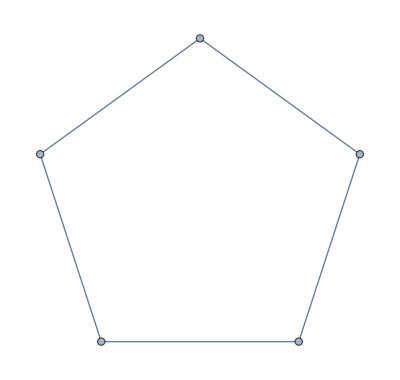

```mathematica
GraphPlot[CycleGraph[5]]
```

It is well known that the complement of the shortest odd hole on 5 vertices is isomorphic to its complement. Thus, let us generate the odd antihole on 7 vertices.

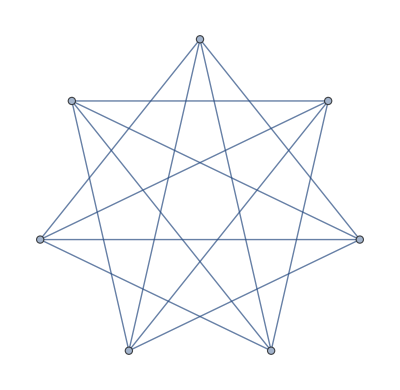

```mathematica
GraphPlot[GraphComplement[CycleGraph[7]]]
```

Let us generate all odd anti-holes up to 20 vertices and put them in a table.

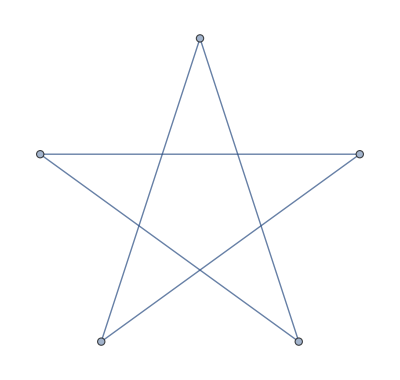
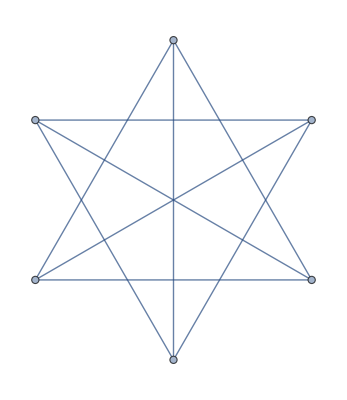
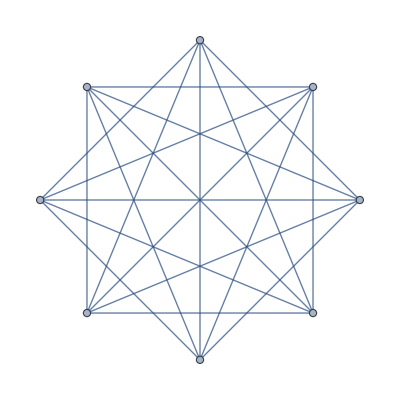
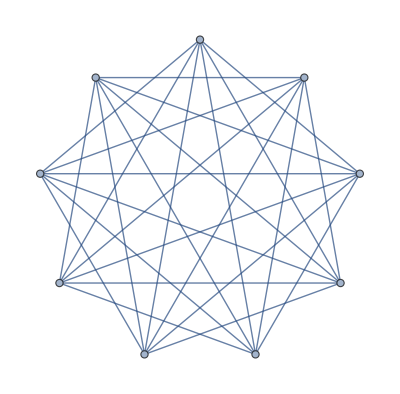
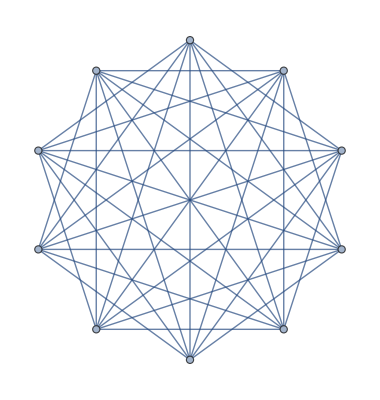
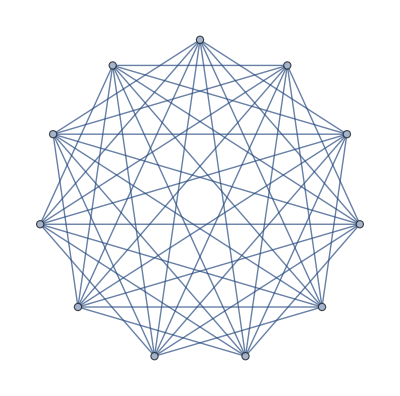
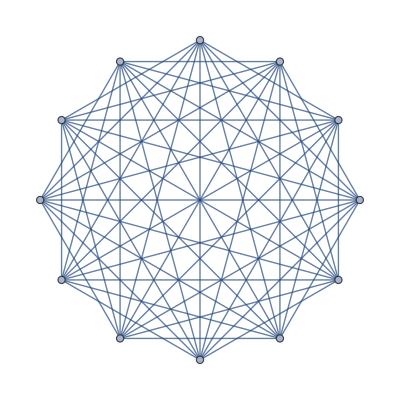
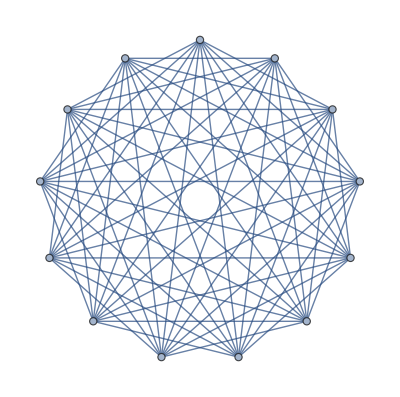
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphComplement[CycleGraph[n]],{n, 5, 20}]
```

## Arithmetic

Of course we can use basic arithmetic in Mathematica. Here are some examples.

```mathematica
1 + 2
```

3

```mathematica
3*4(12+1)*23
```

3588

```mathematica
20/3
```

20/3

Notice that Mathematica always evaluates to the simplest exact form, e.g. 20/3 is not further evaluated. Suppose that we want to get an approximate value. This is simple.

```mathematica
N[20/3]
```

6.66667

Suppose that we want to include more than 5 digits. This is also simple.

```mathematica
N[20/3, 20]
```

6.6666666666666666667

Basic constants are of course builtin .

```mathematica
Pi
```

π

```mathematica
N[Pi, 10]
```

3.141592654

```mathematica
Sqrt[2]
```

√2

```mathematica
N[Sqrt[2], 35]
```

1.4142135623730950488016887242096981

## The Kernel

Mathematica sends the input from our notebook to a backend kernel which does the actually evaluation. We can access the last evaluation as follows.

```mathematica
Pi
```

π

```mathematica
Out[35]
```

π

```mathematica
1 + 1
```

2

```mathematica
Out[37] + 5
```

7

Restarting the kernel is simple as well, e.g. if we want to interrupt a long running calculations. The shortcut is “Option + Dot”.